```mathematica
$Assumptions=P∈ Reals&&-1<=q<=1&&t>0
```

P∈Reals&&-1≤q≤1&&t>0

```mathematica
ExpectedValue[Max[0,1(Exp[#1-1/2t]-1)-P]-Max[0,-(Exp[#1-1/2t]-1)-P]&,NormalDistribution[0,Sqrt[t]]]
```

Piecewise[{{1/2 (-P+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), P≥1&&t>0}, {1/2 (-Erf[(t-2 Log[1-P])/(2 √2 √t)]-Erf[(t+2 Log[1-P])/(2 √2 √t)]+P Erf[(t+2 Log[1-P])/(2 √2 √t)]+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), -1<P<1&&t>0}, {1/2 (-2-P+Erf[(t-2 Log[1-P])/(2 √2 √t)]-Erf[(t+2 Log[1-P])/(2 √2 √t)]+P Erf[(t+2 Log[1-P])/(2 √2 √t)]+2 Erfc[(t-2 Log[1-P])/(2 √2 √t)]), True}}]

```mathematica
g[t_,P_]:=Piecewise[{{1/2 (-P+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), P≥1&&t>0}, {1/2 (-Erf[(t-2 Log[1-P])/(2 √2 √t)]-Erf[(t+2 Log[1-P])/(2 √2 √t)]+P Erf[(t+2 Log[1-P])/(2 √2 √t)]+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), -1<P<1&&t>0}, {1/2 (-2-P+Erf[(t-2 Log[1-P])/(2 √2 √t)]-Erf[(t+2 Log[1-P])/(2 √2 √t)]+P Erf[(t+2 Log[1-P])/(2 √2 √t)]+2 Erfc[(t-2 Log[1-P])/(2 √2 √t)]), True}}]
```

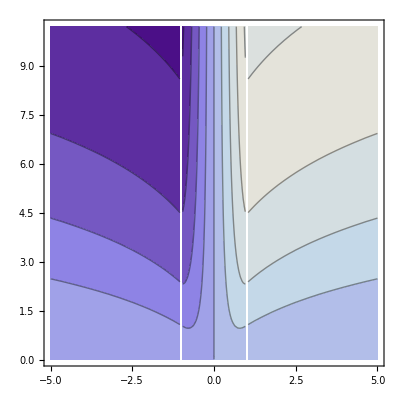

```mathematica
ContourPlot[g[t,P],{P,-5,5},{t,0.01,10.2}]
```

```mathematica
ExpectedValue[Max[0,Sign[-P](Exp[#1-1/2t]-1)+P]&,NormalDistribution[0,Sqrt[t]]]
```

Piecewise[{{1/2 (P+Erf[(t-2 Log[1-P])/(2 √2 √t)]+Erf[(t+2 Log[1-P])/(2 √2 √t)]-P Erf[(t+2 Log[1-P])/(2 √2 √t)]), P<0&&t>0}, {1/2 (P+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), P>0&&t>0}, {0, True}}]

```mathematica
f[t_,P_]:=Piecewise[{{1/2 (P+Erf[(t-2 Log[1-P])/(2 √2 √t)]+Erf[(t+2 Log[1-P])/(2 √2 √t)]-P Erf[(t+2 Log[1-P])/(2 √2 √t)]), P<0&&t>0}, {1/2 (P+Erf[(t-2 Log[1+P])/(2 √2 √t)]+Erf[(t+2 Log[1+P])/(2 √2 √t)]+P Erf[(t+2 Log[1+P])/(2 √2 √t)]), P>0&&t>0}, {0, True}}]
```

```mathematica
Plot3D[f[t,P],{P,-2,2},{t,0.01,20.2}]
```

-Graphics3D-

```mathematica
ExpectedValue[Max[0,(Exp[#1-1/2t]-1)]&,NormalDistribution[0,Sqrt[t]]]
```

Erf[(√t)/(2 √2)]

```mathematica
Erf[(√t)/(2 √2)]/.t->1000000000000000//N
```

General::unfl: Underflow occurred in computation.

1.

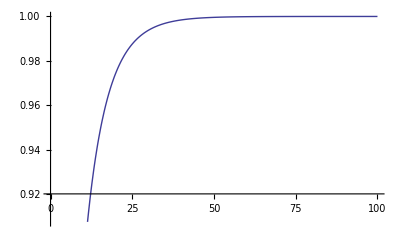

```mathematica
Plot[Erf[(√t)/(2 √2)],{t,0,100}]
```

```mathematica
ExpectedValue[Abs[Exp[#1-1/2t]-1]&,NormalDistribution[0,Sqrt[t]]]
```

2 Erf[(√t)/(2 √2)]